{{te→38.5921}}

38.5921

3.50354

1.57394

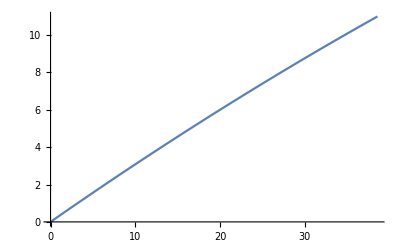

```mathematica
ClearAll["Global`*"]
t0 =.;te=.;
x0=.; xe=.; v0=.; ve=.;
c1=.;c2=.;c3=.;c4=.;

lamda1[t_] := c1;
lamda2[t_] := -c1*t-c2;
a[t_] := c1*t+c2;
v[t_] := (1.0/2.0)*c1*t^2 + c2*t + c3;
x[t_] := (1.0/6.0)*c1*t^3 + (1.0/2.0)*c2*t^2 + c3*t + c4; 

c = Solve[{v[t0] == v0, v[te] == ve, x[t0] == x0, x[te] == xe}, {c1,c2,c3,c4}];
c1 = c1/.c[[1]];c2 = c2/.c[[1]];c3 = c3/.c[[1]];c4 = c4/.c[[1]];

cost[te_]=Integrate[0.5*a[t]^2,{t,t0,te}]+0.5*w*te;
Hte=0.5*a[te]^2+lamda1[te]*v[te]+lamda2[te]*a[te]+0.5*w;

t0=0; w =0.1;
x0 = 150.0;v0=0.0;
xe = 370;ve=11;
(*x0 = 0.0;v0=0.0;
xe = 220;ve=11;*)

tf=NSolve[Hte==0 && te>0,te,Reals]
te=te/.tf[[1]]

cost[te]
cost2[te_]=Integrate[0.5*a[t]^2,{t,t0,te}];
cost2[te]

Plot[v[t],{t,0,te}]
```